```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
MemoryInUse[](*useful function when using many scatterers!*)
```

31918440

```mathematica
Names["MultipleScattering2D`*"]
```

{AttenuationFromListFrequency,CombineWaves,ConvolutionTest,CylindricalWaveFromCoefficients,DrawScatterers,ExportListCylindricalWave,ExportListFrequency,ExportListWaves,FrequencyFromScatterers,GenerateParticles,ImportBoundaryFrequency,ImportListCylindricalWave,ImportListFrequency,ImportListWaves,ListCylindricalWaveDueToImpulse,ListPlotSequence,ListWavesDueToImpulse,MultipleScatteringCoefficients,OutWave,PlotCylindricalWave,rngωFourierOffset,ScatteringCoefficientOperator,SetParametersAndReturnOptions,SingleScattererCoefficientsFromImpulse,StatsFromParticles,TotalWave}

## Two body multiple scattering

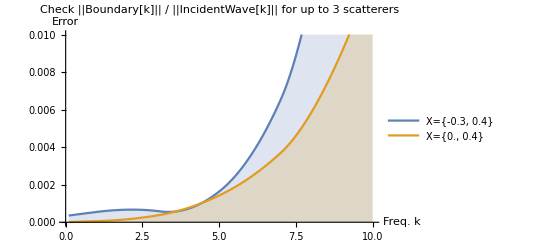

{PrintChecks→True,SourceWave→(Exp[ⅈ #2 #1⟦1⟧]&),BoundaryCondition→Dirchlett,MaxFrequency→10.}

```mathematica
Calculate the response for a given frequency and position;

(*radius of the scatterers*)
radius=0.1; 
(*max number of hankel functions per scatterer*)
N0=2;
(*angular frequency*)
ωs = {6.};

options={
"PrintChecks"-> True,(*will activate different checks for different functions, but is slow!*)
"SourceWave"-> (Exp[I #2 #1[[1]]]&),(*chose a plane wave*)
"BoundaryCondition"-> "Dirchlett"(*"BoundaryCondition"-> "Neumann"*)
};

(*Position of the scatterers and listeners/recievers*)
Xs={{-.3,.4},{0.,.4}};
listeners={{0.,0.},{0.,1}};

(*Calcualted scatterd wave*)         
ClearAll[k1,r2,r1]
 {{{k1,r1}},{{k1,r2}}} = FrequencyFromScatterers[listeners, Xs,radius, N0,ωs,Unevaluated@options];
(*where k1 == ωs[[1]] and ri is the response measured at listeners[[i]] *)

(*Note often if an option is chosen to be default, it is added to your options. For example "MaxFrequency" below*)
options
```

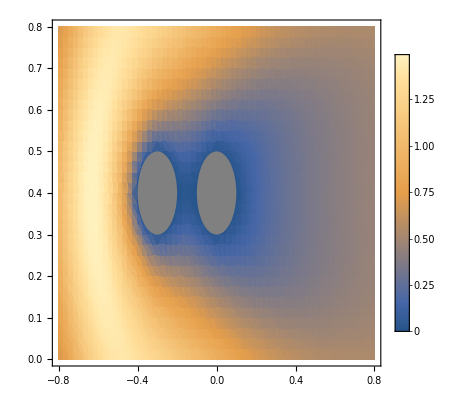

```mathematica
Generate a field plot of the frequency;

(*remove PrintChecks from option, takes too long*)
	options= options[[2;;All]];
(*choose mesh*)
	rngX=Range[-8 radius,8 radius,radius/4];
	rngY=Range[0.,8 radius,radius/4];
(*Calculate response at every mesh point *)
	responses =FrequencyFromScatterers[listeners, Xs,radius, N0,ωs];
(*plot the result*)
	data = Flatten@{listeners[[#]],Abs@responses[[#,1,2]]}&/@Range[Length@responses];
	p1=ListDensityPlot[data,InterpolationOrder->1,PlotLegends->Automatic ];
	p2 = DrawScatterers[Xs,radius];
	Show[p1,p2]
```

For the frequency given, we have mesh t ∈ Range[0, 28.2743,0.310707]

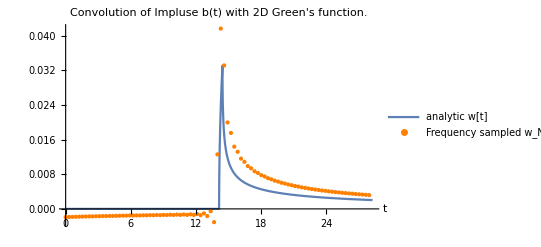

|Wi[k]|_θ: 1.9281

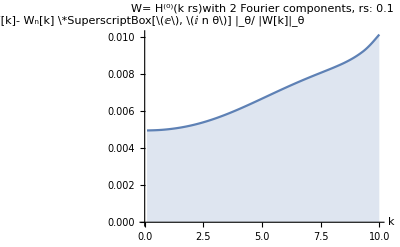

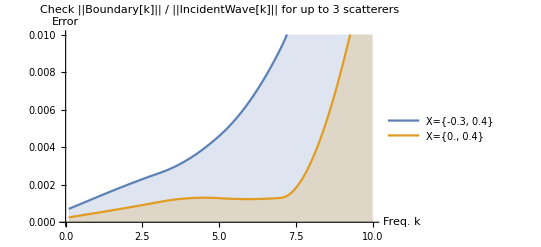

Mesh Size:0.040512

InterpolatingFunction::dmval: Input value {-0.7064,0.7064} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

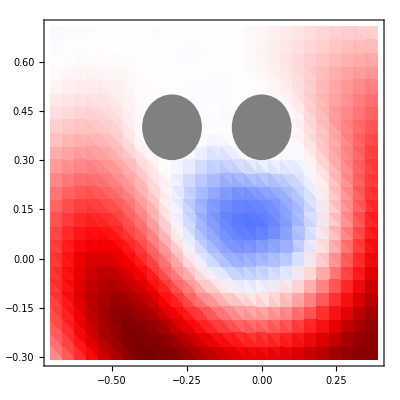

/home/art/Software/Dropbox (The University of Manchester)/study/Scattering/ScatterCylinder/v3/examples/TwoBodyScattering.gif

If[RangeTime,RangeTime/.options,{}]

```mathematica
Calculate field plots of the time repsonse;

options={
"PrintChecks"-> True,
"MaxFrequency"-> 1./radius,
"MaxTime"-> 6,
(*"SaveGIF"-> True,*) (*automatically generate gif*)
(*"SaveData"-> True,*)
"MeshSize"->radius,
"BoundaryCondition"-> "Dirichlet",(*"BoundaryCondition"-> "Neumann",*)
"MaxTimeSamples"-> 4
(*,"MaxRadius"->3*)
};

{{{x0,x1},{y0,y1}},listWaves}= ListWavesDueToImpulse[Xs, radius,N0,options];
(* where the fields where sampled in the box [x0,x1]X[y0,y1]*)

plotSequence= ListPlotSequence[listWaves,options];
listplots= (Show@@#)&/@Thread[{plotSequence,DrawScatterers[Xs,radius]}];
(*Have a look at one of the plots*)
listplots[[3]]
(*Save all plots as a gif*)
Export[NotebookDirectory[]<>"TwoBodyScattering.gif",listplots]
```